```mathematica
Table[Length[Select[all5TreeKeys,ClawGraphQ[allGraphs5[#,"graph"]]&&VertexCount[allGraphs5[#,"graph"]]==k&]],{k,5}]
```

{0,15,75,40,5}

```mathematica
IsNext[k_,m_]:=k+1==m||k==1&&m==5
```

```mathematica
NextI[i_]:=If[i==5,1,i+1]
```

```mathematica
SetOk[set_]:=Block[{anomalies=0,i,next},
For[i=1,i<Length[set],i++,
next=NextI[set[[i]]];
If[set[[i+1]]≠next, anomalies++]
];
next=NextI[set[[Length[set]]]];
If[set[[1]]≠next, anomalies++];
anomalies≤1
]
```

```mathematica
{1,4,5}//Differences
```

{3,1}

```mathematica
SetOk[{1,3,5}]
```

False

```mathematica
SetOk[{1,4}]
```

False

```mathematica
ClawGraphQ[g_]:=If[VertexCount[g]==1,EdgeCount[g]==0,IsomorphicGraphQ[ClawGraph[VertexCount[g]],g]]
```

```mathematica
ContinuousSet[set_]:=Fold[And,Table[SetOk[bucket],{bucket,set}]]
```

```mathematica
ContinuousSet[k_Integer]:=ContinuousSet[allGraphs5[k,"vertexsets"]]
```

```mathematica
Table[Length[Select[all5TreeKeys,ClawGraphQ[allGraphs5[#,"graph"]]&&VertexCount[allGraphs5[#,"graph"]]==k&&ContinuousSet[#]&]],{k,5}]
```

{1,10,30,20,5}

```mathematica
ClawGraphQ[allGraphs5[0,"graph"]]
```

False

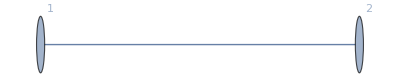

```mathematica
ClawGraph[2]
```

```mathematica
four=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
ClawGraphQ[g]&&VertexCount[g]==4]&]
```

{29646,29322,29214,29178,29166,29162,29920,31438,26850,35976,33156,22312,24408,20794,21492,20052,20040,20036,49194,46182,41644,40126,9094,11190,7576,8274,6978,6870,6818,15400,13882,3038,3736,2764,2332,2284,5134,1246,922,778}

```mathematica
Fold[Join,Table[ListofVars[allGraphs5[k,"colofour"]],{k,four}]]//DeleteDuplicates//Length
```

50

```mathematica
Length[four]
```

40

```mathematica
claw=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
ClawGraphQ[g]]&]
```

{29160,29646,29826,29888,29706,29648,29322,29378,29328,29214,29232,29178,29186,29166,29162,29920,30406,30586,30082,29938,29128,31438,31924,31984,31492,31444,32198,32684,31224,27610,28308,26850,26852,35976,36138,36194,36030,35978,36736,36898,35434,38254,38308,39014,37548,33916,34620,33156,33158,23072,23770,22312,22318,25168,25868,24408,24414,20794,20812,21492,21510,20034,20052,20060,20040,20036,49194,49212,49220,49200,49196,49954,49972,48460,51472,51478,52232,50718,46942,47694,46182,46184,56010,56012,56770,55252,58288,59048,53734,42404,43156,41650,41644,44662,40144,40126,9854,10552,9148,9094,11950,12650,11244,11190,7738,7576,8436,8274,7034,6978,6870,6816,6818,16160,16864,15454,15400,18274,14044,13882,3524,3038,4222,3736,2824,2764,2332,2284,2278,5620,5134,1426,1246,922,778,760}

```mathematica
Fold[Join,Table[ListofVars[allGraphs5[k,"colofour"]],{k,claw}]]//DeleteDuplicates//Length
```

52

```mathematica
Length[claw]
```

136

```mathematica
Table[Map[Labeled[ShowGraph5Least[#],ContinuousSet[#]]&,Select[all5TreeKeys,ClawGraphQ[allGraphs5[#,"graph"]]&&VertexCount[allGraphs5[#,"graph"]]==k&]],{k,5}]
```

{{-Graphics-590481True},{-Graphics-298881True,-Graphics-305861True,-Graphics-319840False,-Graphics-326841True,-Graphics-361940False,-Graphics-368980False,-Graphics-383080False,-Graphics-390141True,-Graphics-492201True,-Graphics-499721True,-Graphics-514780False,-Graphics-522321True,-Graphics-560121True,-Graphics-567701True,-Graphics-582881True},{-Graphics-298262True,-Graphics-297061False,-Graphics-296482True,-Graphics-293781False,-Graphics-293281False,-Graphics-292321False,-Graphics-291862True,-Graphics-304062True,-Graphics-300821False,-Graphics-299382True,-Graphics-291282True,-Graphics-319241False,-Graphics-314920False,-Graphics-314440False,-Graphics-321982True,-Graphics-312241False,-Graphics-276101False,-Graphics-283082True,-Graphics-268522True,-Graphics-361380False,-Graphics-360300False,-Graphics-359781False,-Graphics-367361False,-Graphics-354340False,-Graphics-382541False,-Graphics-375481False,-Graphics-339160False,-Graphics-346201False,-Graphics-331581False,-Graphics-230721False,-Graphics-237701False,-Graphics-223180False,-Graphics-251680False,-Graphics-258682True,-Graphics-244141False,-Graphics-208121False,-Graphics-215102True,-Graphics-200602True,-Graphics-492122True,-Graphics-492001False,-Graphics-491962True,-Graphics-499542True,-Graphics-484602True,-Graphics-514721False,-Graphics-507181False,-Graphics-469421False,-Graphics-476942True,-Graphics-461842True,-Graphics-560102True,-Graphics-552522True,-Graphics-537342True,-Graphics-424042True,-Graphics-431562True,-Graphics-416501False,-Graphics-446621False,-Graphics-401442True,-Graphics-98542True,-Graphics-105522True,-Graphics-91481False,-Graphics-119500False,-Graphics-126502True,-Graphics-112441False,-Graphics-77380False,-Graphics-84361False,-Graphics-70341False,-Graphics-161601False,-Graphics-168641False,-Graphics-154541False,-Graphics-182741False,-Graphics-140441False,-Graphics-35242True,-Graphics-42222True,-Graphics-28241False,-Graphics-56201False,-Graphics-14262True},{-Graphics-296464True,-Graphics-293222False,-Graphics-292141False,-Graphics-291784True,-Graphics-291662False,-Graphics-291624True,-Graphics-299204True,-Graphics-314382False,-Graphics-268504True,-Graphics-359762False,-Graphics-331561False,-Graphics-223122False,-Graphics-244082False,-Graphics-207942False,-Graphics-214924True,-Graphics-200524True,-Graphics-200402False,-Graphics-200364True,-Graphics-491944True,-Graphics-461824True,-Graphics-416444True,-Graphics-401264True,-Graphics-90944True,-Graphics-111902False,-Graphics-75762False,-Graphics-82744True,-Graphics-69781False,-Graphics-68702False,-Graphics-68184True,-Graphics-154002False,-Graphics-138822False,-Graphics-30384True,-Graphics-37364True,-Graphics-27644True,-Graphics-23322False,-Graphics-22841False,-Graphics-51341False,-Graphics-12464True,-Graphics-9222False,-Graphics-7784True},{-Graphics-291608True,-Graphics-200348True,-Graphics-68168True,-Graphics-22788True,-Graphics-7608True}}

```mathematica
Map[Labeled[ShowGraph5Least[#],ContinuousSet[#]]&,allGraphs5TreeKeys]
```

{-Graphics-590481True,-Graphics-582881True,-Graphics-552522True,-Graphics-567701True,-Graphics-560121True,-Graphics-461803True,-Graphics-461842True,-Graphics-476942True,-Graphics-469421False,-Graphics-507181False,-Graphics-522321True,-Graphics-514780False,-Graphics-484602True,-Graphics-499721True,-Graphics-492201True,-Graphics-199365True,-Graphics-199403True,-Graphics-199692False,-Graphics-200293True,-Graphics-200602True,-Graphics-214203True,-Graphics-215102True,-Graphics-207212False,-Graphics-208121False,-Graphics-243842False,-Graphics-244141False,-Graphics-258682True,-Graphics-251680False,-Graphics-222871False,-Graphics-223180False,-Graphics-237701False,-Graphics-230721False,-Graphics-331301False,-Graphics-331581False,-Graphics-346201False,-Graphics-339160False,-Graphics-375481False,-Graphics-390141True,-Graphics-383080False,-Graphics-354340False,-Graphics-368980False,-Graphics-361940False,-Graphics-268213True,-Graphics-268522True,-Graphics-283082True,-Graphics-276101False,-Graphics-312241False,-Graphics-326841True,-Graphics-319840False,-Graphics-291282True,-Graphics-305861True,-Graphics-298881True}

```mathematica
Map[Labeled[ShowGraph5Least[#],ContinuousSet[#]]&,allGraphs5TreeKeys2]
```

{-Graphics-298881True,-Graphics-492201True,-Graphics-560121True,-Graphics-582881True,-Graphics-98542True,-Graphics-200602True,-Graphics-291862True,-Graphics-35242True,-Graphics-268522True,-Graphics-296482True,-Graphics-14262True,-Graphics-291282True,-Graphics-298262True,-Graphics-424042True,-Graphics-461842True,-Graphics-491962True,-Graphics-401442True,-Graphics-484602True,-Graphics-492122True,-Graphics-537342True,-Graphics-552522True,-Graphics-560102True,-Graphics-30384True,-Graphics-68184True,-Graphics-200364True,-Graphics-291624True,-Graphics-7784True,-Graphics-90944True,-Graphics-200524True,-Graphics-291784True,-Graphics-12464True,-Graphics-27644True,-Graphics-268504True,-Graphics-296464True,-Graphics-401264True,-Graphics-416444True,-Graphics-461824True,-Graphics-491944True,-Graphics-7608True,-Graphics-22788True,-Graphics-68168True,-Graphics-200348True,-Graphics-291608True}